```mathematica
SetDirectory[NotebookDirectory[]];SetDirectory["../DataFiles/Super"];
```

## Get Data

```mathematica
data=Import["rep_50lowest_level_500.m"];
```

```mathematica
data0000=Import["rep_0_0_0_0_level_1000.m"];
```

```mathematica
datafund=Import["rep_fundamentals_1000.m"];
data2000=Import["rep_2_0_0_0_level_1000.m"];
```

```mathematica
(*Coefficients for leading order Rademacher Bessel expansions for various representations*)
coefflist=Uncompress[Get["coeff1list.m"]];
```

```mathematica
(*Even Higher for 6 reps [Singlet, 4 fundamentals, symm. traceless]]. Necessary for higher Rademacher*)
coeff1listL=Uncompress[Get["coeff1list110.m"]];
```

```mathematica
(*Coefficients for second Rademacher for 7 reps.*)
coeff2list=Uncompress[Get["coeff2list.m"]];
```

```mathematica
(*Coefficients for third Rademacher for 6 reps*)
coeff3list=Uncompress[Get["coeff3list.m"]];
```

```mathematica
(*Coefficients for fourth Rademacher for 6 reps.*)
coeff4list=Uncompress[Get["coeff4list.m"]];
```

```mathematica
(*Coefficients for fifth Rademacher for 6 reps.*)
coeff5list=Uncompress[Get["coeff5list.m"]];
```

## Definitions

```mathematica
(*Compute dimension of SO(9) rep*)
Dimrep[rep_List]:=Module[{w,g,p,q,r,s},p=rep[[1]];q=rep[[2]];r=rep[[3]];s=rep[[4]];w={p+q+r+s/2,q+r+s/2,r+s/2,s/2};g=Table[{9/2-i},{i,4}];Product[(w[[i]]+g[[i]])/g[[i]],{i,4}]Product[((w[[i]]+g[[i]])^2-(w[[j]]+g[[j]])^2)/(g[[i]]^2-g[[j]]^2),{i,3},{j,i+1,4}]][[1]]
```

```mathematica
(*Result of Inverse Laplace transform*)
BIa[a_,x_]:=Module[{},2Pi (x)^(-1-a) BesselI[1+a,2  π x]]
```

```mathematica
(*Leading Rademacher contribution*)
Repsum1[coeffT_List]:=Sum[BIa[40+2(i-1),x]coeffT[[i]],{i,Length[coeffT]}]
```

```mathematica
(*Second Rademacher.  Variables a and b inserted to test the importance of each term *)Repsum2[coeff2_List,a_:1,b_:1]:=a/2^26 Sum[1/2^i BIa[25+(i-1),x/2]coeff2[[2,i]],{i,Length[coeff2[[2]]]}]+b/2^20 Sum[1/2^i BIa[19+(i-1),x/2]coeff2[[3,i]],{i,Length[coeff2[[3]]]}]
```

```mathematica
(*Third Rademacher contribution.  Variables a-e inserted to test the importance of each term *)Repsum3[coeff3_List,a_:1,b_:1,c_:1,d_:1,e_:1]:=a/3^41 Sum[1/3^i BIa[40+(i-1),x/3]coeff3[[2,i]],{i,Length[coeff3[[2]]]}]+b/3^26 Sum[1/3^i BIa[25+(i-1),x/3]coeff3[[3,i]],{i,Length[coeff3[[3]]]}]+c/3^17 Sum[1/3^i BIa[16+(i-1),x/3]coeff3[[4,i]],{i,Length[coeff3[[4]]]}]+d/3^14 Sum[1/3^i BIa[13+(i-1),x/3]coeff3[[5,i]],{i,Length[coeff3[[5]]]}]+e/3^17 Sum[1/3^i BIa[16+(i-1),x/3]coeff3[[6,i]],{i,Length[coeff3[[6]]]}]
```

```mathematica
(*Fourth Rademacher contribution.  Variables a-f inserted to test the importance of each term.*)
Repsum4[coeff4_List,a_:1,b_:1,c_:1,d_:1,e_:1,f_:1]:=a/4^26 Sum[1/4^i BIa[25+(i-1),x/4]coeff4[[2,i]],{i,Length[coeff4[[2]]]}]+b/4^14 Sum[1/4^i BIa[13+(i-1),x/4]coeff4[[3,i]],{i,Length[coeff4[[3]]]}]+c/4^15 Sum[1/4^i BIa[14+(i-1),x/4]coeff4[[4,i]],{i,Length[coeff4[[4]]]}]+d/4^12 Sum[1/4^i BIa[11+(i-1),x/4]coeff4[[5,i]],{i,Length[coeff4[[5]]]}]+e/4^17 Sum[1/4^i BIa[16+(i-1),x/4]coeff4[[6,i]],{i,Length[coeff4[[6]]]}]+f/4^11 Sum[1/4^i BIa[10+(i-1),x/4]coeff4[[7,i]],{i,Length[coeff4[[7]]]}]
```

```mathematica
(*Generic Rademacher contribution.  Variables a-f inserted to test the importance of each term.*)
Repsum[qq_,coeff_List,t0_List ]:=Module[{a},a=ConstantArray[1,Length[t0]];Sum[a[[j]]/qq^(t0[[j]]+5)Sum[1/qq^i BIa[t0[[j]]+4+(i-1),x/qq]coeff[[j+1,i]],{i,Length[coeff[[j+1]]]}],{j,Length[coeff]-1}]]
```

```mathematica
getreplist[max_]:=Module[{blist,A1,A2,A3,A4,A5,A6,A7,AA},blist={};A1=Table[If[HeavisideTheta[max-p-3q-6r-5s+7+1/2]==1,{p,q,r,s},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1},{r,0,Floor[(max+7)/6]+1},{s,4,Floor[(max+7)/5+1]}];A1=Flatten[A1,3];A2=Table[If[HeavisideTheta[max-p-3q-6r-9+1/2]==1,{p,q,r,3},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1},{r,0,Floor[(max+7)/6]+1}];A2=Flatten[A2,2];A3=Table[If[HeavisideTheta[max-p-3q-6r-5+1/2]==1,{p,q,r,2},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1},{r,0,Floor[(max+7)/6]+1}];A3=Flatten[A3,2];A4=Table[If[HeavisideTheta[max-p-3q-6r-1+1/2]==1,{p,q,r,1},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1},{r,1,Floor[(max+7)/6]+1}];A4=Flatten[A4,2];A5=Table[If[HeavisideTheta[max-p-3q-6r+2+1/2]==1,{p,q,r,0},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1},{r,1,Floor[(max+7)/6]+1}];A5=Flatten[A5,2];A6=Table[If[HeavisideTheta[max-p-3q-2+1/2]==1,{p,q,0,1},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1}];A6=Flatten[A6,1];A7=Table[If[HeavisideTheta[max-p-3q+0+1/2]==1,{p,q,0,0},##&[]],{p,0,max},{q,0,Floor[(max+7)/3]+1}];A7=Flatten[A7,1];AA=Sort[Join[A1,A2,A3,A4,A5,A6,A7]];AA=Join[Drop[AA,-2],{Last[AA]}]]
```

```mathematica
(*Yet another way of writing this since the constant piece always satisfies -1<constant<=0 and the final result has to be an integer*)

SRdd[n_]:=Module[{},Floor[n^4/2160+n^3/36+(109 n^2)/360+(11/12+5/54  Mod[n,3]-1/18  Mod[(-1+n) n,3])n]]
```

## First Rademacher

### Get representation list

```mathematica
(*Go to level 30 to make sure we get the 51 lowest dimensional reps.*)
```

```mathematica
replist=Take[Sort[getreplist[30],Dimrep[#1]<Dimrep[#2]&],51];
```

```mathematica
maxlevel=Length[data];
```

### Plots vs. Leading Rademacher for the first 51 reps up to level 500.

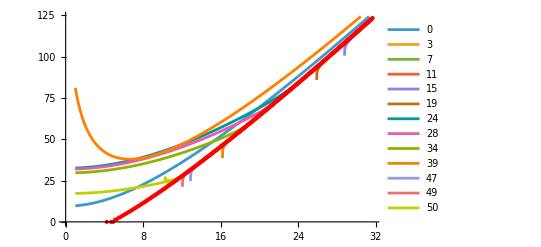

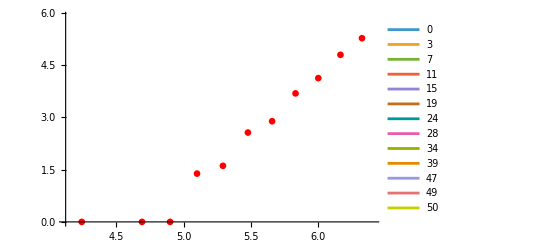

Representation {1, 0, 2, 0}

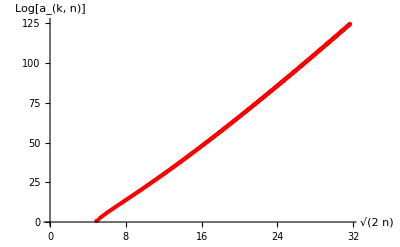

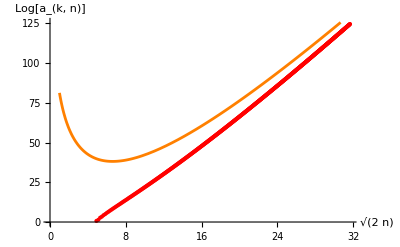

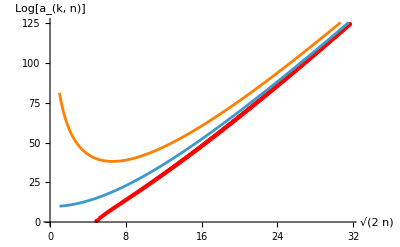

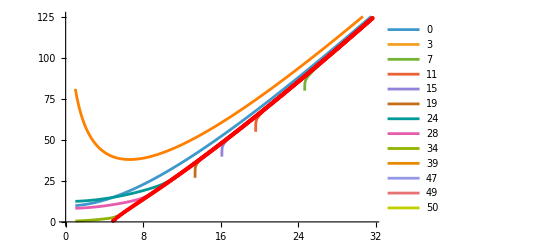

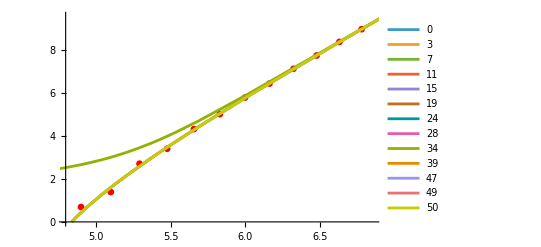

Representation {3, 0, 0, 2}

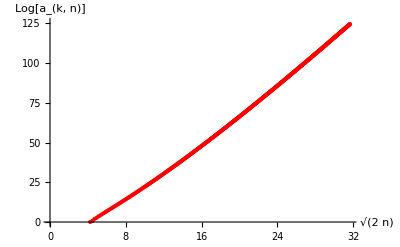

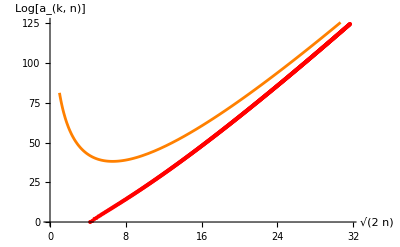

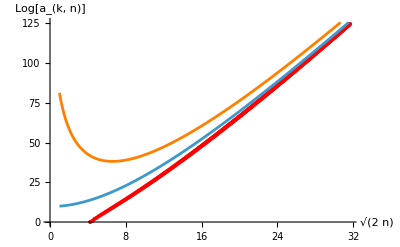

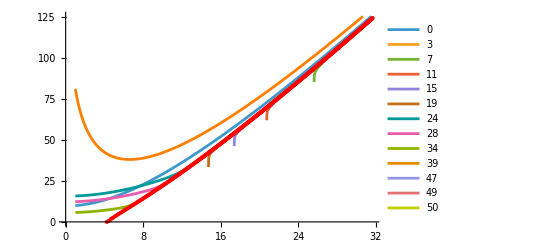

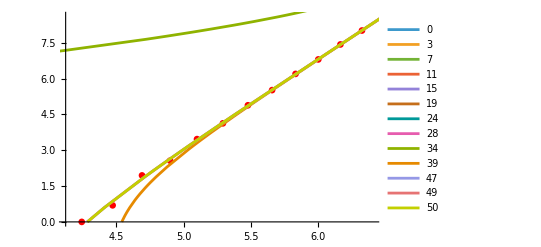

Representation {5, 0, 0, 1}

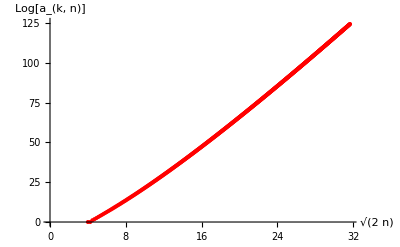

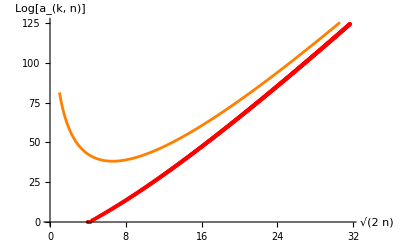

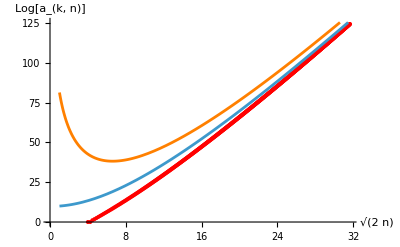

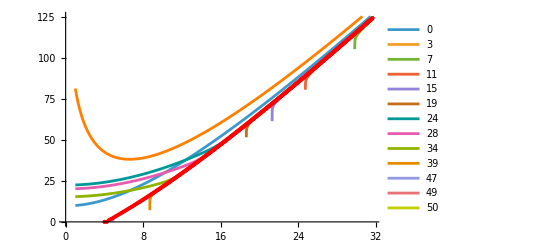

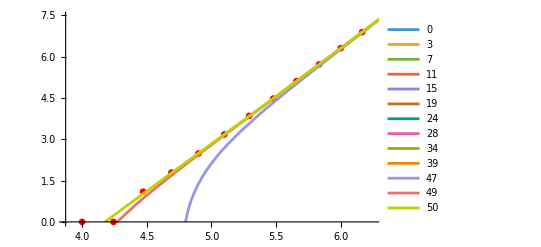

Representation {0, 1, 1, 1}

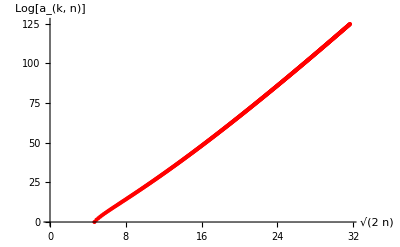

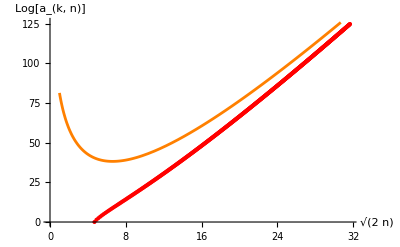

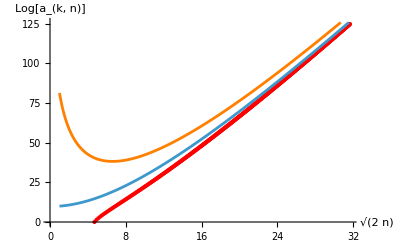

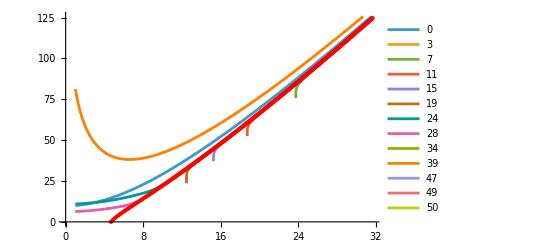

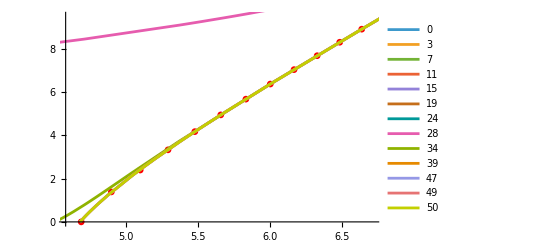

Representation {0, 1, 0, 3}

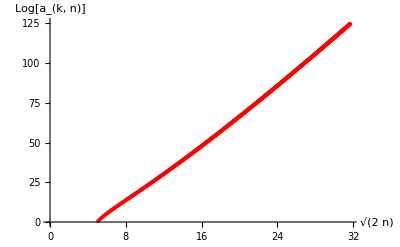

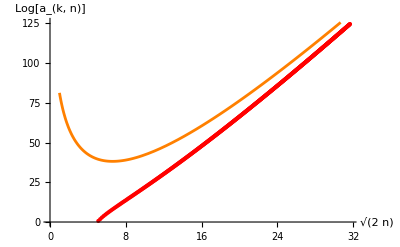

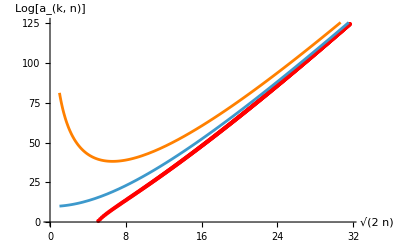

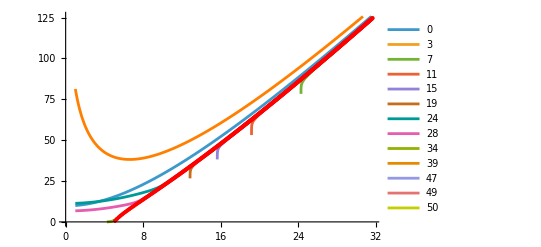

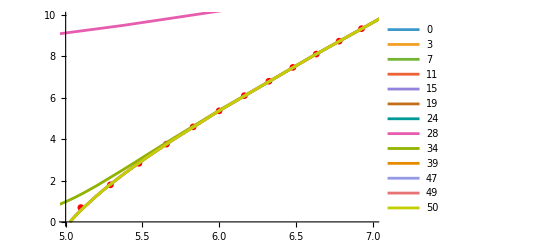

Representation {0, 0, 2, 1}

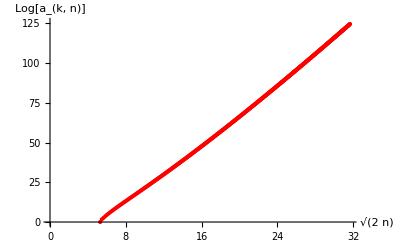

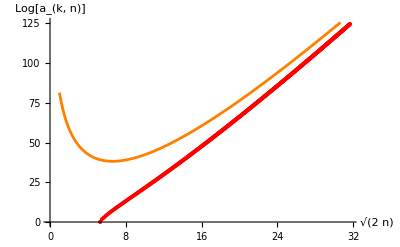

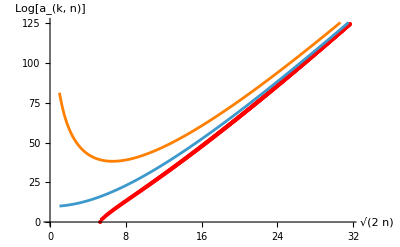

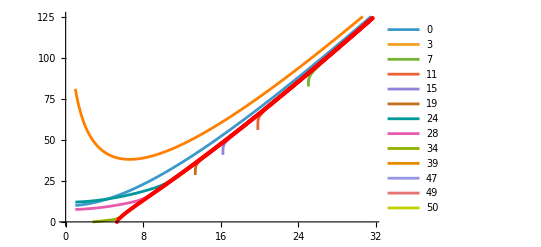

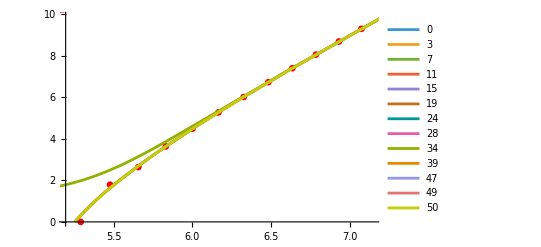

```mathematica
Do[
rep=replist[[i]];posrep=Position[Transpose[coefflist][[1]],rep][[1,1]];
logdata=Table[{√(2(j+1)),Log[data[[j]][rep]]},{j,maxlevel}];bplot=ListPlot[logdata,PlotStyle->Red,AxesLabel->{"√(2  n)","Log[a_(k, n)]"},PlotRange->{{0,√(2(maxlevel+1))},{0,Log[data[[maxlevel]][rep]]+1}}];
Print["Representation "<>ToString[rep]];
Print[Show[bplot]];nz=SelectFirst[Transpose[logdata][[2]],#1>=0&->"Index"];lb=√(2nz+1);ub=√(2nz+25);
bplotzoom=ListPlot[logdata,PlotRange->{{lb,ub},{0,Log[data[[nz+12]][rep]]}},PlotStyle->{Red,PointSize[.012]}];
explist={1,4,8,12,16,20,25,29,35,40,Length[coefflist[[posrep,2]]]-3,Length[coefflist[[posrep,2]]]-1,Length[coefflist[[posrep,2]]]};
BI0=ⅇ^(2 π x)/x^(83/2);bes0=Log[BI0 coefflist[[posrep,2,1]]];bes0plot=Plot[bes0,{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1},PlotStyle->Orange,AxesLabel->{"√(2  n)","Log[a_(k, n)]"}];Print[Show[bes0plot,bplot]];
besTab=ParallelTable[Log[Sum[BIa[40+2(i-1),x]coefflist[[posrep,2,i]],{i,j}]],{j,explist}];
besplot=Plot[besTab,{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1},PlotLegends->explist-1];
besplot1=Plot[besTab[[1]],{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1}];Print[Show[bplot,besplot1,bes0plot]];
Print[Show[besplot,bplot,bes0plot]];
Print[Show[bplotzoom,besplot]],
{i,Length[replist]}]
```

### Plots vs. Leading Rademacher for the scalar and the four fundamentals up to level 1000.

```mathematica
replist={{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0},{2,0,0,0}};
```

```mathematica
data=Association[Table[i->Join[data0000[[i]],datafund[[i]],data2000[[i]]],{i,Length[data0000]}]];
```

```mathematica
data[[10]]
```

```mathematica
maxlevel=Length[data];
```

```mathematica
Do[
rep=replist[[i]];posrep=Position[Transpose[coefflist][[1]],rep][[1,1]];
logdata=Table[{√(2(j+1)),Log[data[[j]][rep]]},{j,maxlevel}];bplot=ListPlot[logdata,PlotStyle->Red,AxesLabel->{"√(2  n)","Log[a_(k, n)]"},PlotRange->{{0,√(2(maxlevel+1))},{0,Log[data[[maxlevel]][rep]]+1}}];
Print["Representation "<>ToString[rep]<>", Dimension="<>ToString[Dimrep[rep]]];
Print[Show[bplot]];nz=SelectFirst[Transpose[logdata][[2]],#1>=0&->"Index"];lb=√(2nz+1);ub=√(2nz+25);
bplotzoom=ListPlot[logdata,PlotRange->{{lb,ub},{0,Log[data[[nz+12]][rep]]}},PlotStyle->{Red,PointSize[.012]}];
explist={1,8,15,22,29,36,51};
BI0=ⅇ^(2 π x)/x^(83/2);bes0=Log[BI0 coefflist[[posrep,2,1]]];bes0plot=Plot[bes0,{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1},PlotStyle->Orange,AxesLabel->{"√(2  n)","Log[a_(k, n)]"}];besTab=ParallelTable[Log[Sum[BIa[40+2(k-1),x]coefflist[[posrep,2,k]],{k,j}]],{j,explist}];
Print[Show[bes0plot,bplot]];
besplot1=Plot[besTab[[1]],{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1}];Print[Show[bplot,besplot1,bes0plot]];
besplot=Plot[besTab,{x,1,√(2(maxlevel+1))},PlotRange->{0,Log[data[[maxlevel]][rep]]+1},PlotLegends->explist-1];
Print[Show[besplot,bplot,bes0plot]];
Print[Show[bplotzoom,besplot]],
{i,Length[replist]}]
```

## Second Rademacher

The second Rademacher coefficient comes from either ω1,ω2,ω3=0,π  and ω4=+- π/2 plus permutations,  or
ω1,ω2,ω3=+- π/2, ω4=0,π  plus permutations.

```mathematica
max=200;replist={{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0},{2,0,0,0}};
data=Association[Table[i->Join[data0000[[i]],datafund[[i]],data2000[[i]]],{i,Length[data0000]}]];
```

```mathematica
Do[
rep=replist[[i]];
Print["Representation "<>ToString[rep]<>", Dimension="<>ToString[Dimrep[rep]]];
coeffT=coeff1listL[[Position[Transpose[coeff1listL][[1]],rep][[1,1]]]][[2]];
coeff2=coeff2list[[Position[Transpose[coeff2list][[1]],rep][[1,1]]]];
rad12list=ParallelTable[{j,((data[[j]][rep]-Round[Repsum1[coeffT]+(-I)(-1)^(j+1) Repsum2[coeff2,1,1]/.{x->√(2(j+1))}]))},{j,max}];
Print[ListPlot[rad12list]];
,{i,Length[replist]}]
```

## Third Rademacher

The third Rademacher term comes from (ω1,ω2,ω3,ω4)=(0,0,0,0),(0,0,2π/3), (0,0,π/3,π/3),(0,π/3,π/3,2π/3),(π/3,π/3,π/3,π/3) plus permutations and shifts by +/- π that keep ω1+ω2+ω3+ω4 =2 n/3 π.  This give 5 distinct terms.

```mathematica
max=200;replist={{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0},{2,0,0,0}};
data=Association[Table[i->Join[data0000[[i]],datafund[[i]],data2000[[i]]],{i,Length[data0000]}]];
```

```mathematica
Do[
rep=replist[[i]];
Print["Representation "<>ToString[rep]<>", Dimension="<>ToString[Dimrep[rep]]];
coeffT=coeff1listL[[Position[Transpose[coeff1listL][[1]],rep][[1,1]]]][[2]];
coeff2=coeff2list[[Position[Transpose[coeff2list][[1]],rep][[1,1]]]];
coeff3=coeff3list[[Position[Transpose[coeff3list][[1]],rep][[1,1]]]];
rad123list=ParallelTable[{j,((data[[j]][rep]-Round[Repsum1[coeffT]+(-I)(-1)^(j+1) Repsum2[coeff2,1,1]+2Re[Exp[-2π/3(j+1+1)I]Repsum3[coeff3]]/.{x->√(2(j+1))}]))},{j,max}];
Print[ListPlot[rad123list]];
,{i,Length[replist]}]
```

## Fourth Rademacher

The fourth Rademacher comes from (ω1,ω2,ω3,ω4)=(n1π/4,n2π/4,n3π/4,n4π/4) with n1+n2+n3+n4 odd.  This gives 6 distinct choices.

```mathematica
max=200;replist={{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0},{2,0,0,0}};
data=Association[Table[i->Join[data0000[[i]],datafund[[i]],data2000[[i]]],{i,Length[data0000]}]];
```

```mathematica
Do[
rep=replist[[i]];
Print["Representation "<>ToString[rep]<>", Dimension="<>ToString[Dimrep[rep]]];
coeffT=coeff1listL[[Position[Transpose[coeff1listL][[1]],rep][[1,1]]]][[2]];
coeff2=coeff2list[[Position[Transpose[coeff2list][[1]],rep][[1,1]]]];
coeff3=coeff3list[[Position[Transpose[coeff3list][[1]],rep][[1,1]]]];
coeff4=coeff4list[[Position[Transpose[coeff4list][[1]],rep][[1,1]]]];
rad1234list=ParallelTable[{j,((data[[j]][rep]-Round[Repsum1[coeffT]+(-I)(-1)^(j+1) Repsum2[coeff2,1,1]+2Re[Exp[-2π/3(j+1+1)I]Repsum3[coeff3]]+2Re[Exp[-2π/4(j+1+3/2)I]Repsum4[coeff4]]/.{x->√(2(j+1))}]))},{j,max}];
Print[ListPlot[rad1234list]];
,{i,Length[replist]}]
```

## Fifth Rademacher

The fifth Rademacher comes from (ω1,ω2,ω3,ω4)=(n1π/4,n2π/4,n3π/4,n4π/4) with n1+n2+n3+n4 odd.  This gives 15 distinct choices.  We also must sum over d=-1 and d=-2.

```mathematica
max=200;replist={{0,0,0,0},{1,0,0,0},{0,0,0,1},{0,1,0,0},{0,0,1,0},{2,0,0,0}};
data=Association[Table[i->Join[data0000[[i]],datafund[[i]],data2000[[i]]],{i,Length[data0000]}]];
```

```mathematica
Do[
rep=replist[[i]];
Print["Representation "<>ToString[rep]<>", Dimension="<>ToString[Dimrep[rep]]];
coeffT=coeff1listL[[Position[Transpose[coeff1listL][[1]],rep][[1,1]]]][[2]];
coeff2=coeff2list[[Position[Transpose[coeff2list][[1]],rep][[1,1]]]];
coeff3=coeff3list[[Position[Transpose[coeff3list][[1]],rep][[1,1]]]];
coeff4=coeff4list[[Position[Transpose[coeff4list][[1]],rep][[1,1]]]];
posrep=Position[Transpose[coeff5list[[1]]][[1]],rep][[1,1]];
(* Starting powers of t -4*)
t0={36,21,21,12,12,10,9,5,5,9,12,6,4,6,12};
coeff51=coeff5list[[1,posrep]];coeff52=coeff5list[[2,posrep]];
rad12345list=ParallelTable[{j,((data[[j]][rep]-Round[Repsum1[coeffT]+(-I)(-1)^(j+1) Repsum2[coeff2,1,1]+2Re[Exp[-2π/3(j+1+1)I]Repsum3[coeff3]]+2Re[Exp[-2π/4(j+1+3/2)I]Repsum4[coeff4]]+2Re[Exp[-2π/5(j+1+2)I]Repsum[5,coeff51,t0]+Exp[-4π/5(j+1+1/2)I]Repsum[5,coeff52,t0]]/.{x->√(2(j+1))}]))},{j,max}];
Print[ListPlot[rad12345list]];
,{i,Length[replist]}]
```